# Noise Analysis of Absorption image

GUO, Zhichao

guozc12@gmail.com

Dajun Wang’s Cold Atom Lab @The Chinese University of Hong Kong

2020.06.09 - Ver_1.0
2020.10.17 - Ver_1.1
2021.04.14 - Ver_2.0

Abstract

In this note, we mainly talk about the signal and noise of the absorption imaging method(AIM). Combined with the knowledge from the noise analysis of camera, we discuss the dominant effect and parameters when choosing a camera for AIM.

### Global function

```mathematica
ClearAll["Global`*"];
```

## Absorption image theory

### Absorption image

When doing absorption image, we typically take three images, noted as:

C_in(x,y) as input light distribution on the atom

C_out(x,y) as output(after absorption) light

C_bg(x,y) as the background

formula for calculating OD as following

OD(x,y)=n_col(x,y)σ_0^*=Log[(C_in(x,y)-C_bg(x,y))/(C_out(x,y)-C_bg(x,y))]+(C_in(x,y)-C_out(x,y))/C_sat^eff

where

C(x,y)=I(x,y)×A_pix/M^2×λ/(h c)×T×QE×τ×1/ADC

I(x,y) is the intensity distribution of light on atom

A_pix is the pixel size of camera, A_pix/M^2 is the real pixel size with counting magnification of image system.

λ is the probe light wavelength

T is the transmission rate of the image system

QE is the quantum efficiency of the camera

ADC is the ADC conversion efficiency of the camera

τ is the exposure time

### Noise analysis

The Noise can be written as

σ_OD^2=((∂OD)/(∂C_in))^2 σ_C_in^2+((∂OD)/(∂C_out))^2 σ_C_out^2+((∂OD)/(∂C_bg))^2 σ_C_bg^2
=(1/C_sat^eff+1/(C_in-C_bg))^2 σ_C_in^2+(1/C_sat^eff+1/(C_out-C_bg))^2 σ_C_out^2+(1/(C_in-C_bg)-1/(C_out-C_bg))^2 σ_C_bg^2

Then, The Signal to Noise ratio is

SNR=(Log[(C_in-C_bg)/(C_out-C_bg)]+(C_in-C_out)/C_sat^eff)/(√((1/C_sat^eff+1/(C_in-C_bg))^2 σ_C_in^2+(1/C_sat^eff+1/(C_out-C_bg))^2 σ_C_out^2+(1/(C_in-C_bg)-1/(C_out-C_bg))^2 σ_C_bg^2))

Put noise formula into the above SNR, we have

SNR=(Log[(C_in-C_bg)/(C_out-C_bg)]+(C_in-C_out)/C_sat^eff)/(√(((1/C_sat^eff+1/(C_in-C_bg))^2+(1/C_sat^eff+1/(C_out-C_bg))^2+(1/(C_in-C_bg)-1/(C_out-C_bg))^2)σ_readout^2+(1/C_sat^eff+1/(C_in-C_bg))^2 σ_(in-signal)^2+(1/C_sat^eff+1/(C_out-C_bg))^2 σ_(out-signal)^2+(1/(C_in-C_bg)-1/(C_out-C_bg))^2 σ_(bg-signal)^2))

Re-write σ_(in-signal) as σ_in, σ_(out-signal) as σ_out, and σ_(bg-signal)=0, we have

SNR=(Log[(C_in-C_bg)/(C_out-C_bg)]+(C_in-C_out)/C_sat^eff)/(√(((1/C_sat^eff+1/(C_in-C_bg))^2+(1/C_sat^eff+1/(C_out-C_bg))^2+(1/(C_in-C_bg)-1/(C_out-C_bg))^2)(σ_readout^2+σ_dark^2)+(1/C_sat^eff+1/(C_in-C_bg))^2 σ_in^2+(1/C_sat^eff+1/(C_out-C_bg))^2 σ_out^2))

#### Numerical

```mathematica
SNR[Cin_,Cout_,Csat_,Cbg_,σrd_,σdark_,σclc_,σin_,σout_,F_,G_]:=(Log[(Cin-Cbg)/(Cout-Cbg)]+(Cin-Cout)/Csat)/(√(((1/Csat+1/(Cin-Cbg))^2+(1/Csat+1/(Cout-Cbg))^2+(1/(Cin-Cbg)-1/(Cout-Cbg))^2)(σrd^2+F^2 G^2(σdark^2+σclc^2))+F^2 G^2((1/Csat+1/(Cin-Cbg))^2 σin^2+(1/Csat+1/(Cout-Cbg))^2 σout^2)));
```

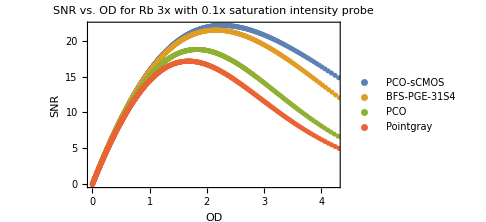

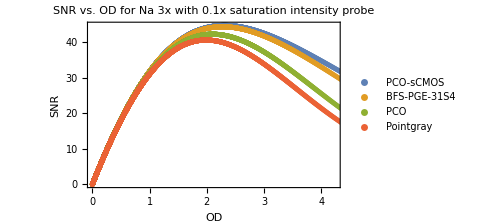

```mathematica
F=1;  (*For CCD and CMOS*)
G=1; (*For CCD and CMOS*)
σdark=0.001;
σclc=0;
CRsat=200;   
τ=50;
Csat=CRsat*τ;
Cbg=√(σrd^2+F^2 G^2(σdark^2+σclc^2));
Cintemp=0.1*CRsat*τ;
Plot[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G],SNR[Cintemp,Cout,Csat,0,σrd,0,0,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}];
ListPlot[Table[Table[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}],{σrd,{1.1,2.3,6,8.3}}],Frame->True,PlotStyle->PointSize[0.01],PlotLegends->{"PCO-sCMOS","BFS-PGE-31S4","PCO","Pointgray"},PlotLabel->Style["SNR vs. OD for Rb 3x with 0.1x saturation intensity probe",FontSize->15],FrameLabel->{Style["OD",FontFamily->"Times New Roman",FontSize->20],Style["SNR",FontFamily->"Times New Roman",FontSize->20]},ImageSize->Medium]
F=1;  (*For CCD and CMOS*)
G=1; (*For CCD and CMOS*)
σdark=0.001;
σclc=0;
CRsat=800;   
τ=50;
Csat=CRsat*τ;
Cbg=√(σrd^2+F^2 G^2(σdark^2+σclc^2));
Cintemp=0.1*CRsat*τ;
Plot[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G],SNR[Cintemp,Cout,Csat,0,σrd,0,0,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}];
ListPlot[Table[Table[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}],{σrd,{1.1,2.3,6,8.3}}],Frame->True,PlotStyle->PointSize[0.01],PlotLegends->{"PCO-sCMOS","BFS-PGE-31S4","PCO","Pointgray"},PlotLabel->Style["SNR vs. OD for Na 3x with 0.1x saturation intensity probe",FontSize->15],FrameLabel->{Style["OD",FontFamily->"Times New Roman",FontSize->20],Style["SNR",FontFamily->"Times New Roman",FontSize->20]},ImageSize->Medium]
```

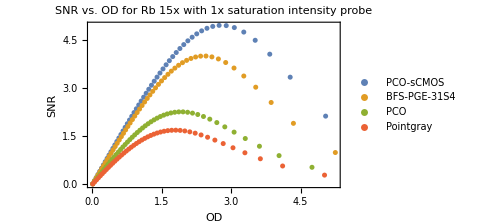

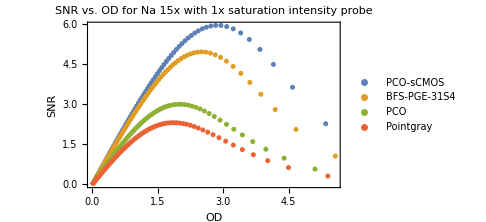

```mathematica
F=1;  (*For CCD and CMOS*)
G=1; (*For CCD and CMOS*)
σdark=0.001;
σclc=0;
CRsat=5.42;   
τ=10;
Csat=CRsat*τ;
Cbg=√(σrd^2+F^2 G^2(σdark^2+σclc^2));
Cintemp=1*CRsat*τ;
Plot[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G],SNR[Cintemp,Cout,Csat,0,σrd,0,0,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}];
ListPlot[Table[Table[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}],{σrd,{1.1,2.3,6,8.3}}],Frame->True,PlotStyle->PointSize[0.01],PlotLegends->{"PCO-sCMOS","BFS-PGE-31S4","PCO","Pointgray"},PlotLabel->Style["SNR vs. OD for Rb 15x with 1x saturation intensity probe",FontSize->15],FrameLabel->{Style["OD",FontFamily->"Times New Roman",FontSize->20],Style["SNR",FontFamily->"Times New Roman",FontSize->20]},ImageSize->Medium]
F=1;  (*For CCD and CMOS*)
G=1; (*For CCD and CMOS*)
σdark=0.001;
σclc=0;
CRsat=24.2;   
τ=3;
Csat=CRsat*τ;
Cbg=√(σrd^2+F^2 G^2(σdark^2+σclc^2));
Cintemp=1*CRsat*τ;
Plot[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G],SNR[Cintemp,Cout,Csat,0,σrd,0,0,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}];
ListPlot[Table[Table[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}],{σrd,{1.1,2.3,6,8.3}}],Frame->True,PlotStyle->PointSize[0.01],PlotLegends->{"PCO-sCMOS","BFS-PGE-31S4","PCO","Pointgray"},PlotLabel->Style["SNR vs. OD for Na 15x with 1x saturation intensity probe",FontSize->15],FrameLabel->{Style["OD",FontFamily->"Times New Roman",FontSize->20],Style["SNR",FontFamily->"Times New Roman",FontSize->20]},ImageSize->Medium]
```

Conclusion is that, for 3x system, the improvement is limited. However, for 15x system (reach the resolution limit case, NOT HAVE TO be 15x) we will get an improvement of about 3 times than before.

##### List of camera we use now

### find the limitation of detection

```mathematica
F=1;  (*For CCD and CMOS*)
G=1; (*For CCD and CMOS*)
σdark=0.001;
σclc=0;
CRsat=200; 
τ=50;
Csat=CRsat*τ;
Cbg=√(2.3^2+F^2 G^2(σdark^2+σclc^2));
Cintemp=x*CRsat*τ;
(*Plot[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G],SNR[Cintemp,Cout,Csat,0,σrd,0,0,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}];*)
(*ListPlot[Table[Table[{Log[(Cintemp-Cbg)/(Cout-Cbg)]+(Cintemp-Cout)/Csat,SNR[Cintemp,Cout,Csat,Cbg,σrd,σdark,σclc,√Cintemp,√Cout,F,G]},{Cout,1,Cintemp}],{σrd,{1.1,2.3,6,8.3}}],Frame->True,PlotStyle->PointSize[0.01],PlotLegends->{"PCO-sCMOS","BFS-PGE-31S4","PCO","Pointgray"},PlotLabel->Style["SNR vs. OD for Rb 3x with 0.1x saturation intensity probe",FontSize->15],FrameLabel->{Style["OD",FontFamily->"Times New Roman",FontSize->20],Style["SNR",FontFamily->"Times New Roman",FontSize->20]},ImageSize->Medium]*)
```

```mathematica
ListPointPlot3D[Flatten[#,0]&@Table[Table[{Log[(x*CRsat*τ-Cbg)/(Cout-Cbg)]+(x*CRsat*τ-Cout)/Csat,x,SNR[x*CRsat*τ,Cout,Csat,Cbg,2.3,σdark,σclc,√(x*CRsat*τ),√Cout,F,G]},{Cout,0.8*x*CRsat*τ,x*CRsat*τ,1}],{x,0.1,3,0.1}],PlotRange->All]
```

-Graphics3D-

```mathematica
Solve[Log[(Cin-Cbg)/(Cout-Cbg)]+(Cin-Cout)/Csat==OD,Cout]/.{Cin->3000,OD->1,Cbg->5,Csat->8000}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Cout→Cbg+Csat ProductLog[-((Cbg-Cin) ⅇ^(-Cbg/Csat+Cin/Csat-OD))/Csat]}}

```mathematica
N[Cbg+Csat ProductLog[-((Cbg-Cin) ⅇ^(-Cbg/Csat+Cin/Csat-OD))/Csat]/.{Cin->3000,OD->1,Cbg->5,Csat->8000}]
```

1357.85

```mathematica
SNR[Cin_,Cout_,Csat_,Cbg_,σrd_,σdark_,σclc_,σin_,σout_,F_,G_]:=(Log[(Cin-Cbg)/(Cout-Cbg)]+(Cin-Cout)/Csat)/(√(((1/Csat+1/(Cin-Cbg))^2+(1/Csat+1/(Cout-Cbg))^2+(1/(Cin-Cbg)-1/(Cout-Cbg))^2)(σrd^2+F^2 G^2(σdark^2+σclc^2))+F^2 G^2((1/Csat+1/(Cin-Cbg))^2 σin^2+(1/Csat+1/(Cout-Cbg))^2 σout^2)));
```

```mathematica
F=1;  (*For CCD and CMOS*)
G=1; (*For CCD and CMOS*)
σdark=0.001;
σclc=0;
Cbg=√(2.3^2+F^2 G^2(σdark^2+σclc^2));
```

```mathematica
CRsat=200; 
τ=50;
Csat=CRsat*τ;
Cintemp=x*CRsat*τ;
```

```mathematica
{Log[(Cin-Cbg)/(Cout-Cbg)]+(Cin-Cout)/Csat,x,SNR[Cin,Cout,Csat,Cbg,2.3,σdark,σclc,√Cin,√Cout,F,G]}
```